# Pure shear

## explore the numerical shear to a snapshot

### numerical function

```mathematica
numdericalϵ[allPoints_List,box_List,ddx_,ka_,kp_,pa_,pp_]:=Module[{Vareas0,Vperis0,Vareas1,Vperis1,VareasI,VperisI,copies,translations,translatedCopies,allPointsPBD,cellIndex,cellIndex0,cellIndex1,strainfor,strainback,vm,vm1,vm0,allPointsPBD0,allPointsPBD1,min,max,voronoiPolygons,voronoiPolygons1,voronoiPolygons0},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
strainfor={{1+ddx,0},{0,1/(1+ddx)}};
strainback={{1-ddx,0},{0,1/(1-ddx)}};
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
allPointsPBD=Select[allPointsPBD,-3<#[[1]]<box[[1]]+3&&-3<#[[2]]<box[[2]]+3&];
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
VareasI=PropertyValue[{vm,2},MeshCellMeasure];
VperisI=RegionMeasure/@(MeshPrimitives[vm,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
allPointsPBD0=strainfor.#&/@allPointsPBD;
vm0=VoronoiMesh[allPointsPBD0,{{min,max},{min,max}}];
voronoiPolygons0=MeshPrimitives[vm0,2];
cellIndex0=Table[Position[Table[RegionMember[voronoiPolygons0[[j]],allPointsPBD0[[i]]],{j,Length[allPointsPBD0]}],True][[1,1]],{i,Length[allPoints]}];
Vareas0=PropertyValue[{vm0,2},MeshCellMeasure];
Vperis0=RegionMeasure/@(MeshPrimitives[vm0,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
allPointsPBD1=strainback.#&/@allPointsPBD;
vm1=VoronoiMesh[allPointsPBD1,{{min+0.001*min,max+0.001*max},{min,max}}];
Vareas1=PropertyValue[{vm1,2},MeshCellMeasure];
Vperis1=RegionMeasure/@(MeshPrimitives[vm1,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
voronoiPolygons1=MeshPrimitives[vm1,2];
cellIndex1=Table[Position[Table[RegionMember[voronoiPolygons1[[j]],allPointsPBD1[[i]]],{j,Length[allPointsPBD1]}],True][[1,1]],{i,Length[allPoints]}];
Table[{(ka(Vareas0[[cellIndex0[[i]]]]-pa)^2+kp(Vperis0[[cellIndex0[[i]]]]-pp)^2-ka(Vareas1[[cellIndex1[[i]]]]-pa)^2-kp(Vperis1[[cellIndex1[[i]]]]-pp)^2)/(2*ddx),(ka(Vareas0[[cellIndex0[[i]]]]-pa)^2+kp(Vperis0[[cellIndex0[[i]]]]-pp)^2+ka(Vareas1[[cellIndex1[[i]]]]-pa)^2+kp(Vperis1[[cellIndex1[[i]]]]-pp)^2-2*(ka(VareasI[[cellIndex[[i]]]]-pa)^2+kp(VperisI[[cellIndex[[i]]]]-pp)^2))/ddx/ddx},{i,1,Length[allPoints]}]
];
```

```mathematica
numdericalEnergyStressϵ[allPoints_List,box_List,ddx_,ka_,kp_,pa_,pp_]:=Module[{Vareas0,Vperis0,Vareas1,Vperis1,VareasI,VperisI,copies,translations,translatedCopies,allPointsPBD,cellIndex,cellIndex0,cellIndex1,strainfor,strainback,vm,vm1,vm0,allPointsPBD0,allPointsPBD1,min,max,voronoiPolygons,voronoiPolygons1,voronoiPolygons0},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
strainfor={{1+ddx,0},{0,1/(1+ddx)}};
strainback={{1-ddx,0},{0,1/(1-ddx)}};
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
allPointsPBD=Select[allPointsPBD,-3<#[[1]]<box[[1]]+3&&-3<#[[2]]<box[[2]]+3&];
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
VareasI=PropertyValue[{vm,2},MeshCellMeasure];
VperisI=RegionMeasure/@(MeshPrimitives[vm,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
allPointsPBD0=strainfor.#&/@allPointsPBD;
vm0=VoronoiMesh[allPointsPBD0,{{min,max},{min,max}}];
voronoiPolygons0=MeshPrimitives[vm0,2];
cellIndex0=Table[Position[Table[RegionMember[voronoiPolygons0[[j]],allPointsPBD0[[i]]],{j,Length[allPointsPBD0]}],True][[1,1]],{i,Length[allPoints]}];
Vareas0=PropertyValue[{vm0,2},MeshCellMeasure];
Vperis0=RegionMeasure/@(MeshPrimitives[vm0,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
allPointsPBD1=strainback.#&/@allPointsPBD;
vm1=VoronoiMesh[allPointsPBD1,{{min+0.001*min,max+0.001*max},{min,max}}];
Vareas1=PropertyValue[{vm1,2},MeshCellMeasure];
Vperis1=RegionMeasure/@(MeshPrimitives[vm1,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
voronoiPolygons1=MeshPrimitives[vm1,2];
cellIndex1=Table[Position[Table[RegionMember[voronoiPolygons1[[j]],allPointsPBD1[[i]]],{j,Length[allPointsPBD1]}],True][[1,1]],{i,Length[allPoints]}];
Table[{(ka(Vareas0[[cellIndex0[[i]]]]-pa)^2+kp(Vperis0[[cellIndex0[[i]]]]-pp)^2-ka(Vareas1[[cellIndex1[[i]]]]-pa)^2-kp(Vperis1[[cellIndex1[[i]]]]-pp)^2)/(2*ddx),(ka(Vareas0[[cellIndex0[[i]]]]-pa)^2+kp(Vperis0[[cellIndex0[[i]]]]-pp)^2+ka(Vareas1[[cellIndex1[[i]]]]-pa)^2+kp(Vperis1[[cellIndex1[[i]]]]-pp)^2-2*(ka(VareasI[[cellIndex[[i]]]]-pa)^2+kp(VperisI[[cellIndex[[i]]]]-pp)^2))/ddx/ddx},{i,1,Length[allPoints]}]
];
```

```mathematica
numdericalCellg[allPoints_List,box_List,ddx_,ka_,kp_,pa_,pp_]:=Module[{Vareas0,Vperis0,Vareas1,Vperis1,VareasI,VperisI,copies,translations,translatedCopies,allPointsPBD,cellIndex,cellIndex0,cellIndex1,strainfor,strainback,vm,vm1,vm0,allPointsPBD0,allPointsPBD1,min,max,voronoiPolygons,voronoiPolygons1,voronoiPolygons0},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
strainfor={{1,ddx},{0,1}};
strainback={{1,-ddx},{0,1}};
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
allPointsPBD=Select[allPointsPBD,-3<#[[1]]<box[[1]]+3&&-3<#[[2]]<box[[2]]+3&];
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
VareasI=PropertyValue[{vm,2},MeshCellMeasure];
VperisI=RegionMeasure/@(MeshPrimitives[vm,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
allPointsPBD0=strainfor.#&/@allPointsPBD;
vm0=VoronoiMesh[allPointsPBD0,{{min,max},{min,max}}];
voronoiPolygons0=MeshPrimitives[vm0,2];
cellIndex0=Table[Position[Table[RegionMember[voronoiPolygons0[[j]],allPointsPBD0[[i]]],{j,Length[allPointsPBD0]}],True][[1,1]],{i,Length[allPoints]}];
Vareas0=PropertyValue[{vm0,2},MeshCellMeasure];
Vperis0=RegionMeasure/@(MeshPrimitives[vm0,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
allPointsPBD1=strainback.#&/@allPointsPBD;
vm1=VoronoiMesh[allPointsPBD1,{{min+0.001*min,max+0.001*max},{min,max}}];
Vareas1=PropertyValue[{vm1,2},MeshCellMeasure];
Vperis1=RegionMeasure/@(MeshPrimitives[vm1,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
voronoiPolygons1=MeshPrimitives[vm1,2];
cellIndex1=Table[Position[Table[RegionMember[voronoiPolygons1[[j]],allPointsPBD1[[i]]],{j,Length[allPointsPBD1]}],True][[1,1]],{i,Length[allPoints]}];
Table[{(ka(Vareas0[[cellIndex0[[i]]]]-pa)^2+kp(Vperis0[[cellIndex0[[i]]]]-pp)^2-ka(Vareas1[[cellIndex1[[i]]]]-pa)^2-kp(Vperis1[[cellIndex1[[i]]]]-pp)^2)/(2*ddx),(ka(Vareas0[[cellIndex0[[i]]]]-pa)^2+kp(Vperis0[[cellIndex0[[i]]]]-pp)^2+ka(Vareas1[[cellIndex1[[i]]]]-pa)^2+kp(Vperis1[[cellIndex1[[i]]]]-pp)^2-2*(ka(VareasI[[cellIndex[[i]]]]-pa)^2+kp(VperisI[[cellIndex[[i]]]]-pp)^2))/ddx/ddx},{i,1,Length[allPoints]}]
];
```

### analytical functions

```mathematica
(*Cross product for 2d vectors*)
Cross2d[r1_,r2_]:=r1[[1]]r2[[2]]-r1[[2]]r2[[1]]
(*The vertex position given the three adjecent cell positions*)
voro[ri_,rj_,rk_]:=Module[{rij,rjk,rik,cross,d,α,β,γ},
rij=ri-rj;
rjk=rj-rk;
rik=ri-rk;

cross=Cross2d[rij,rjk];
d=2*cross*cross;

α=(rjk.rjk)*(rij.rik)/d;
β=-(rik.rik)*(rij.rjk)/d;
γ=(rij.rij)*(rik.rjk)/d;

α*ri+β*rj+γ*rk
];
```

```mathematica
ri={rix,riy}
rj={rjx,rjy}
rk={rkx,rky}
```

{rix,riy}

{rjx,rjy}

{rkx,rky}

```mathematica
hijk=voro[ri,rj,rk];
den=(rjx*rky-rjy*rkx)^3;
```

```mathematica
(*Analytical dirivatives of dhdr and dhdr*)
```

```mathematica
v1dri[r1_,r2_,r3_]:=(({{D[hijk[[1]],rix], D[hijk[[1]],riy]}, {D[hijk[[2]],rix], D[hijk[[2]],riy]}}))/.{rix->r1[[1]],riy->r1[[2]],rjx->r2[[1]],rjy->r2[[2]],rkx->r3[[1]],rky->r3[[2]]}
```

```mathematica
v2drirj[r1_,r2_,r3_]:={{{D[D[hijk[[1]],rix],rjx],D[D[hijk[[2]],rix],rjx]},
{D[D[hijk[[1]],riy],rjx],D[D[hijk[[2]],riy],rjx]}},
{{D[D[hijk[[1]],rix],rjy],D[D[hijk[[2]],rix],rjy]},
{D[D[hijk[[1]],riy],rjy],D[D[hijk[[2]],riy],rjy]}}}/.{rix->r1[[1]],riy->r1[[2]],rjx->r2[[1]],rjy->r2[[2]],rkx->r3[[1]],rky->r3[[2]]};
```

```mathematica
v2driri[r1_,r2_,r3_]:={{{D[D[hijk[[1]],rix],rix],D[D[hijk[[2]],rix],rix]},
{D[D[hijk[[1]],riy],rix],D[D[hijk[[2]],riy],rix]}},
{{D[D[hijk[[1]],rix],riy],D[D[hijk[[2]],rix],riy]},
{D[D[hijk[[1]],riy],riy],D[D[hijk[[2]],riy],riy]}}}/.{rix->r1[[1]],riy->r1[[2]],rjx->r2[[1]],rjy->r2[[2]],rkx->r3[[1]],rky->r3[[2]]};
```

```mathematica
D[D[1/(1+ϵ),ϵ],ϵ]/.{ϵ->0}
D[1/(1+ϵ),ϵ]/.{ϵ->0}
```

2

-1

```mathematica
test={{{111,112},{211,212}},{{121,122},{221,222}}};
(test[[;;,;;,1]].{x1,y1}).{x2,y2}
```

x2 (111 x1+211 y1)+(121 x1+221 y1) y2

```mathematica
test={{{111,112},{121,122}},{{211,212},{221,222}}};
(test[[;;,;;,1]].{x2,y2}).{x1,y1}
```

x1 (111 x2+121 y2)+y1 (211 x2+221 y2)

```mathematica
(*Analytical dirivatives of dhdg and d2hdgdg*)
```

```mathematica
dridg={riy,0};
drjdg={rjy,0};
drkdg={rky,0};
(*dh2dgdg[r1_,r2_,r3_]:=(v2drirj[r1,r2,r3].{r2[[2]],0}).{r1[[2]],0}+(v2drirj[r1,r3,r2].{r3[[2]],0}).{r1[[2]],0}+(v2driri[r1,r2,r3].{r1[[2]],0}).{r1[[2]],0}+(v2drirj[r2,r1,r3].{r1[[2]],0}).{r2[[2]],0}+(v2drirj[r2,r3,r1].{r3[[2]],0}).{r2[[2]],0}+(v2driri[r2,r1,r3].{r2[[2]],0}).{r2[[2]],0}+(v2drirj[r3,r1,r2].{r1[[2]],0}).{r3[[2]],0}+(v2drirj[r3,r2,r1].{r2[[2]],0}).{r3[[2]],0}+(v2driri[r3,r1,r2].{r3[[2]],0}).{r3[[2]],0};*)
dh2dgdg[r1_,r2_,r3_]:={(v2drirj[r1,r2,r3][[1,1,1]]r2[[2]])r1[[2]]+(v2drirj[r1,r3,r2][[1,1,1]]r3[[2]])r1[[2]]+(v2driri[r1,r2,r3][[1,1,1]]r1[[2]])r1[[2]]+(v2drirj[r2,r1,r3][[1,1,1]]r1[[2]])r2[[2]]+(v2drirj[r2,r3,r1][[1,1,1]]r3[[2]])r2[[2]]+(v2driri[r2,r1,r3][[1,1,1]]r2[[2]])r2[[2]]+(v2drirj[r3,r1,r2][[1,1,1]]r1[[2]])r3[[2]]+(v2drirj[r3,r2,r1][[1,1,1]]r2[[2]])r3[[2]]+(v2driri[r3,r1,r2][[1,1,1]]r3[[2]])r3[[2]],(v2drirj[r1,r2,r3][[1,1,2]]r2[[2]])r1[[2]]+(v2drirj[r1,r3,r2][[1,1,2]]r3[[2]])r1[[2]]+(v2driri[r1,r2,r3][[1,1,2]]r1[[2]])r1[[2]]+(v2drirj[r2,r1,r3][[1,1,2]]r1[[2]])r2[[2]]+(v2drirj[r2,r3,r1][[1,1,2]]r3[[2]])r2[[2]]+(v2driri[r2,r1,r3][[1,1,2]]r2[[2]])r2[[2]]+(v2drirj[r3,r1,r2][[1,1,2]]r1[[2]])r3[[2]]+(v2drirj[r3,r2,r1][[1,1,2]]r2[[2]])r3[[2]]+(v2driri[r3,r1,r2][[1,1,2]]r3[[2]])r3[[2]]};
dh2dϵdϵ[r1_,r2_,r3_]:={(v2driri[r1,r2,r3][[;;,;;,1]].{r1[[1]],-r1[[2]]}).{r1[[1]],-r1[[2]]}+(v2drirj[r1,r2,r3][[;;,;;,1]].{r1[[1]],-r1[[2]]}).{r2[[1]],-r2[[2]]}+(v2drirj[r1,r3,r2][[;;,;;,1]].{r1[[1]],-r1[[2]]}).{r3[[1]],-r3[[2]]}+
(v2driri[r2,r3,r1][[;;,;;,1]].{r2[[1]],-r2[[2]]}).{r2[[1]],-r2[[2]]}+(v2drirj[r2,r3,r1][[;;,;;,1]].{r2[[1]],-r2[[2]]}).{r3[[1]],-r3[[2]]}+(v2drirj[r2,r1,r3][[;;,;;,1]].{r2[[1]],-r2[[2]]}).{r1[[1]],-r1[[2]]}+(v2driri[r3,r2,r1][[;;,;;,1]].{r3[[1]],-r3[[2]]}).{r3[[1]],-r3[[2]]}+(v2drirj[r3,r2,r1][[;;,;;,1]].{r3[[1]],-r3[[2]]}).{r2[[1]],-r2[[2]]}+(v2drirj[r3,r1,r2][[;;,;;,1]].{r3[[1]],-r3[[2]]}).{r1[[1]],-r1[[2]]},(v2driri[r1,r2,r3][[;;,;;,2]].{r1[[1]],-r1[[2]]}).{r1[[1]],-r1[[2]]}+(v2drirj[r1,r2,r3][[;;,;;,2]].{r1[[1]],-r1[[2]]}).{r2[[1]],-r2[[2]]}+(v2drirj[r1,r3,r2][[;;,;;,2]].{r1[[1]],-r1[[2]]}).{r3[[1]],-r3[[2]]}+
(v2driri[r2,r3,r1][[;;,;;,2]].{r2[[1]],-r2[[2]]}).{r2[[1]],-r2[[2]]}+(v2drirj[r2,r3,r1][[;;,;;,2]].{r2[[1]],-r2[[2]]}).{r3[[1]],-r3[[2]]}+(v2drirj[r2,r1,r3][[;;,;;,2]].{r2[[1]],-r2[[2]]}).{r1[[1]],-r1[[2]]}+(v2driri[r3,r2,r1][[;;,;;,2]].{r3[[1]],-r3[[2]]}).{r3[[1]],-r3[[2]]}+(v2drirj[r3,r2,r1][[;;,;;,2]].{r3[[1]],-r3[[2]]}).{r2[[1]],-r2[[2]]}+(v2drirj[r3,r1,r2][[;;,;;,2]].{r3[[1]],-r3[[2]]}).{r1[[1]],-r1[[2]]}}+(v1dri[r1,r2,r3].{0,2r1[[2]]})+(v1dri[r2,r1,r3].{0,2r2[[2]]})+(v1dri[r3,r1,r2].{0,2r3[[2]]});
```

```mathematica
dhdg[r1_,r2_,r3_]:=(v1dri[r1,r2,r3].{r1[[2]],0})+(v1dri[r2,r1,r3].{r2[[2]],0})+(v1dri[r3,r1,r2].{r3[[2]],0});
```

```mathematica
dhdϵ[r1_,r2_,r3_]:=(v1dri[r1,r2,r3].{r1[[1]],-r1[[2]]})+(v1dri[r2,r1,r3].{r2[[1]],-r2[[2]]})+(v1dri[r3,r1,r2].{r3[[1]],-r3[[2]]});
```

```mathematica
(*For C++*)
r1={r1x,r1y};r2={r2x,r2y};r3={r3x,r3y};
```

```mathematica
CForm[Simplify[dhdϵ[r1,r2,r3]/.{r1x->0,r1y->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

List((-(r3y*(r2x*r2x)) + 3*r3y*(r2y*r2y) + r2y*(r3x*r3x) - 3*r2y*(r3y*r3y))/(2*r2y*r3x - 2*r2x*r3y),
   (3*r3x*(r2x*r2x) - r3x*(r2y*r2y) - 3*r2x*(r3x*r3x) + r2x*(r3y*r3y))/(2*r2y*r3x - 2*r2x*r3y))

```mathematica
CForm[Simplify[dh2dϵdϵ[r1,r2,r3]/.{r1x->0,r1y->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

List((6*r2y*(r2y - r3y)*r3y)/(-(r2y*r3x) + r2x*r3y),
   (3*r3x*(r2x*r2x) + r3x*(r2y*r2y) - 3*r2x*(r3x*r3x) - r2x*(r3y*r3y))/(r2y*r3x - r2x*r3y))

```mathematica
(*Numerical test*)
p1={15.764422379230995,17.23195769060852};p2={16.240740458209697,16.83431037696828};p3={15.803192711415326,16.385277852647548};
```

```mathematica
(*This verifies dhdϵ and d2hdϵdϵ*)
strainfor={{1+0.0001,0},{0,1/(1+0.0001)}};
strainback={{1-0.0001,0},{0,1/(1-0.0001)}};
hForward=voro[strainfor.p1,strainfor.p2,strainfor.p3];
hback=voro[strainback.p1,strainback.p2,strainback.p3];
originalh=voro[p1,p2,p3];
(hback+hForward-2*originalh)/0.0001^2
-(hback-hForward)/0.0002
```

{-2.33861,33.6619}

{16.5959,-16.7684}

```mathematica
dh2dϵdϵ[p1,p2,p3]
dhdϵ[p1,p2,p3]
```

{-2.33861,33.6619}

{16.5959,-16.7684}

```mathematica
(*calculate perimetes and areas given the positions of all the vertices*)
peri[hv_List]:=Sum[Sqrt[(hv[[i]]-hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]]).(hv[[i]]-hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]])],{i,1,Length[hv]}];

area[hv_List]:=Sum[0.5*Cross2d[hv[[i]],hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]]],{i,1,Length[hv]}];
```

```mathematica
energy[hv_List,KA_,KP_,PA_,PP_]:=Module[{dedhx,dedhy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
KP*(peri[hv]-PP)^2+KA*(area[hv]-PA)^2
]
```

```mathematica
(*This is the 1st derivative of e w.r.t. h*)
dedhGeneral[hv_List,KA_,KP_,PA_,PP_]:=Module[{dedhx,dedhy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
dedhx=(-1. hiLasty+1. hiNexty) KA (a-PA)+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP);
dedhy=(-1. hiLastx+1. hiNextx) KA (PA-a)+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP);
{dedhx,dedhy}
]
```

```mathematica
(*This is the generalized function for de2dhidhj*)

de2dhihjxx[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2xx,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2xx=2 ((-0.5 hiLasty+0.5 hiNexty)^2 KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)))^2 KP+(-(-hiLastx+hix)^2/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))+1/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))-(-hiNextx+hix)^2/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))+1/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP))];
If[j==2,

de2xx=2 ((-0.5 hiy+0.5 hjNexty) (-0.5 hiLasty+0.5 hjy) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hiy-hjy)^2 KP (p-PP))];
If[j==Length[hv],
de2xx=2 ((0.5 hiy-0.5 hjLasty) (0.5 hiNexty-0.5 hjy) KA+((-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hiy-hjy)^2 KP (p-PP))];
If[!(j==1||j==2||j==Length[hv]),

de2xx=2 (-0.5 hiLasty+0.5 hiNexty) (-0.5 hjLasty+0.5 hjNexty) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2xx
];
de2dhihjxy[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2xy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2xy=2 ((0.5 hiLastx-0.5 hiNextx) (-0.5 hiLasty+0.5 hiNexty) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP+(-((-hiLastx+hix) (-hiLasty+hiy))/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))-((-hiNextx+hix) (-hiNexty+hiy))/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))) KP (p-PP))];
If[j==2,

de2xy=2 (0.5 hix-0.5 hjNextx) (-0.5 hiLasty+0.5 hjy) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP- KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[j==Length[hv],
de2xy=2 (-0.5 hix+0.5 hjLastx) (0.5 hiNexty-0.5 hjy) KA+2 ((-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP+KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[!(j==1||j==2||j==Length[hv]),

de2xy=2 (-0.5 hiLasty+0.5 hiNexty) (0.5 hjLastx-0.5 hjNextx) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2xy
];
de2dhihjyx[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2yx,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2yx=2 ((0.5 hiLastx-0.5 hiNextx) (-0.5 hiLasty+0.5 hiNexty) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP+(-((-hiLastx+hix) (-hiLasty+hiy))/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))-((-hiNextx+hix) (-hiNexty+hiy))/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))) KP (p-PP))];
If[j==2,

de2yx=2 (-0.5 hiy+0.5 hjNexty) (0.5 hiLastx-0.5 hjx) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP+ KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[j==Length[hv],
de2yx=2 (0.5 hiy-0.5 hjLasty) (-0.5 hiNextx+0.5 hjx) KA+2 ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) ((-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) KP-KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[!(j==1||j==2||j==Length[hv]),

de2yx=2 (0.5 hiLastx-0.5 hiNextx) (-0.5 hjLasty+0.5 hjNexty) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2yx
];
de2dhihjyy[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2yy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2yy=2 ((-0.5 hiLastx+0.5 hiNextx)^2 KA+((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)))^2 KP+(-(-hiLasty+hiy)^2/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))+1/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))-(-hiNexty+hiy)^2/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))+1/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP))];
If[j==2,

de2yy=2 ((0.5 hix-0.5 hjNextx) (0.5 hiLastx-0.5 hjx) KA+((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hix-hjx)^2 KP (p-PP))];
If[j==Length[hv],
de2yy=2 ((-0.5 hix+0.5 hjLastx) (-0.5 hiNextx+0.5 hjx) KA+((-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hix-hjx)^2 KP (p-PP))];
If[!(j==1||j==2||j==Length[hv]),

de2yy=2 (0.5 hiLastx-0.5 hiNextx) (0.5 hjLastx-0.5 hjNextx) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2yy
];
de2dhdhGeneral[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{},
{{de2dhihjxx[hv,j,KA,KP,PA,PP],de2dhihjxy[hv,j,KA,KP,PA,PP]},{de2dhihjyx[hv,j,KA,KP,PA,PP],de2dhihjyy[hv,j,KA,KP,PA,PP]}}
]
```

```mathematica
Simplify[dhdϵ[r1,r2,r3]]
```

{(r2y r3x^2+3 r1y^2 (r2y-r3y)-r2x^2 r3y+3 r2y^2 r3y-3 r2y r3y^2+r1x^2 (-r2y+r3y)+r1y (r2x^2-3 r2y^2-r3x^2+3 r3y^2))/(2 (r1y (r2x-r3x)+r2y r3x-r2x r3y+r1x (-r2y+r3y))),(3 r1x^2 (r2x-r3x)+3 r2x^2 r3x-r2y^2 r3x-3 r2x r3x^2+r1y^2 (-r2x+r3x)+r2x r3y^2+r1x (-3 r2x^2+r2y^2+3 r3x^2-r3y^2))/(2 (r1y (r2x-r3x)+r2y r3x-r2x r3y+r1x (-r2y+r3y)))}

```mathematica
Simplify[dh2dϵdϵ[r1,r2,r3]]
```

{(6 (r1y-r2y) (r1y-r3y) (r2y-r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(3 r1x^2 (r2x-r3x)+r1y^2 (r2x-r3x)+3 r2x^2 r3x+r2y^2 r3x-3 r2x r3x^2-r2x r3y^2+r1x (-3 r2x^2-r2y^2+3 r3x^2+r3y^2))/(r1y (r2x-r3x)+r2y r3x-r2x r3y+r1x (-r2y+r3y))}

```mathematica
(*These are the analytical forms for dhdgamma and d2hdgamma2*)
dhdϵGeneral[r1_List,r2_List,r3_List]:=Module[{r1x,r1y,r2x,r2y,r3x,r3y},
r1x=r1[[1]];r1y=r1[[2]];r2x=r2[[1]];r2y=r2[[2]];r3x=r3[[1]];r3y=r3[[2]];
{(r2y r3x^2+3 r1y^2 (r2y-r3y)-r2x^2 r3y+3 r2y^2 r3y-3 r2y r3y^2+r1x^2 (-r2y+r3y)+r1y (r2x^2-3 r2y^2-r3x^2+3 r3y^2))/(2 (r1y (r2x-r3x)+r2y r3x-r2x r3y+r1x (-r2y+r3y))),(3 r1x^2 (r2x-r3x)+3 r2x^2 r3x-r2y^2 r3x-3 r2x r3x^2+r1y^2 (-r2x+r3x)+r2x r3y^2+r1x (-3 r2x^2+r2y^2+3 r3x^2-r3y^2))/(2 (r1y (r2x-r3x)+r2y r3x-r2x r3y+r1x (-r2y+r3y)))}
];

d2hdϵdϵGeneral[r1_List,r2_List,r3_List]:=Module[{r1x,r1y,r2x,r2y,r3x,r3y},
r1x=r1[[1]];r1y=r1[[2]];r2x=r2[[1]];r2y=r2[[2]];r3x=r3[[1]];r3y=r3[[2]];
{(6 (r1y-r2y) (r1y-r3y) (r2y-r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(3 r1x^2 (r2x-r3x)+r1y^2 (r2x-r3x)+3 r2x^2 r3x+r2y^2 r3x-3 r2x r3x^2-r2x r3y^2+r1x (-3 r2x^2-r2y^2+3 r3x^2+r3y^2))/(r1y (r2x-r3x)+r2y r3x-r2x r3y+r1x (-r2y+r3y))}
];
(*These are the analytical forms for dhdgamma and d2hdgamma2*)
dhdgGeneral[r1_List,r2_List,r3_List]:=Module[{r1x,r1y,r2x,r2y,r3x,r3y},
r1x=r1[[1]];r1y=r1[[2]];r2x=r2[[1]];r2y=r2[[2]];r3x=r3[[1]];r3y=r3[[2]];
{(r1x r1y (r2y-r3y)+r2y (r2x-r3x) r3y+r1y (-r2x r2y+r3x r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(-2 r2x r2y r3x+r2y r3x^2-r2x^2 r3y-r2y^2 r3y+2 r2x r3x r3y+r2y r3y^2+r1x^2 (-r2y+r3y)+r1y^2 (-r2y+r3y)+2 r1x (r2x r2y+r1y (-r2x+r3x)-r3x r3y)+r1y (r2x^2+r2y^2-r3x^2-r3y^2))/(2 (-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y))}
];
d2hdgdgGeneral[r1_List,r2_List,r3_List]:=Module[{r1x,r1y,r2x,r2y,r3x,r3y},
r1x=r1[[1]];r1y=r1[[2]];r2x=r2[[1]];r2y=r2[[2]];r3x=r3[[1]];r3y=r3[[2]];
{((r1y-r2y) (r1y-r3y) (r2y-r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(-r2y^2 r3x+r1y^2 (-r2x+r3x)-2 r2x r2y r3y+2 r2y r3x r3y+r2x r3y^2+r1x (r2y^2-r3y^2)+2 r1y (r2x r2y-r3x r3y+r1x (-r2y+r3y)))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y)}
];
```

```mathematica
(*Now this is to calculate de2dgammadgamma for cell i*)
d2eidϵdϵGeneral[allPoints_List,vList_List,ri_,neilist_List,KA_,KP_,PA_,PP_]:=Module[{},
Sum[Sum[de2dhdhGeneral[RotateLeft[vList,i],j,KA,KP,PA,PP].dhdϵGeneral[ri,allPoints[[neilist[[If[j+i==Length[vList],Length[vList],Mod[j+i,Length[vList]]]]]]],allPoints[[neilist[[If[j+1+i==Length[vList]||j+1+i==2*Length[vList],Length[vList],Mod[j+1+i,Length[vList]]]]]]]].dhdϵGeneral[ri,allPoints[[neilist[[If[1+i==Length[vList],Length[vList],Mod[1+i,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{j,1,Length[vList]}]+dedhGeneral[RotateLeft[vList,i],KA,KP,PA,PP].d2hdϵdϵGeneral[ri,allPoints[[neilist[[If[1+i==Length[vList],Length[vList],Mod[1+i,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{i,0,Length[vList]-1}]
];
```

```mathematica
(*Now this is to calculate dedgamma for cell i*)
deidϵGeneral[allPoints_List,vList_List,ri_,neilist_List,KA_,KP_,PA_,PP_]:=Module[{},
Sum[dedhGeneral[RotateLeft[vList,i],KA,KP,PA,PP].dhdϵGeneral[ri,allPoints[[neilist[[If[i+1==Length[vList],Length[vList],Mod[i+1,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList]||2+i==2*Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{i,0,Length[vList]-1}]
];
```

```mathematica
(*Now this is to calculate de2dgammadgamma for cell i*)
d2eidgdgGeneral[allPoints_List,vList_List,ri_,neilist_List,KA_,KP_,PA_,PP_]:=Module[{},
Sum[Sum[de2dhdhGeneral[RotateLeft[vList,i],j,KA,KP,PA,PP].dhdgGeneral[ri,allPoints[[neilist[[If[j+i==Length[vList],Length[vList],Mod[j+i,Length[vList]]]]]]],allPoints[[neilist[[If[j+1+i==Length[vList]||j+1+i==2*Length[vList],Length[vList],Mod[j+1+i,Length[vList]]]]]]]].dhdgGeneral[ri,allPoints[[neilist[[If[1+i==Length[vList],Length[vList],Mod[1+i,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{j,1,Length[vList]}]+dedhGeneral[RotateLeft[vList,i],KA,KP,PA,PP].d2hdgdgGeneral[ri,allPoints[[neilist[[If[1+i==Length[vList],Length[vList],Mod[1+i,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{i,0,Length[vList]-1}]
]
```

```mathematica
(*Now this is to calculate dedgamma for cell i*)
deidgGeneral[allPoints_List,vList_List,ri_,neilist_List,KA_,KP_,PA_,PP_]:=Module[{},
Sum[dedhGeneral[RotateLeft[vList,i],KA,KP,PA,PP].dhdgGeneral[ri,allPoints[[neilist[[If[i+1==Length[vList],Length[vList],Mod[i+1,Length[vList]]]]]]],allPoints[[neilist[[If[2+i==Length[vList]||2+i==2*Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{i,0,Length[vList]-1}]
]
```

```mathematica
(*This gives the neighbor list of cell i in a counterclock-wise order and this neighbor list aligns with the vertex id list*)
```

```mathematica
reorderCCWIndices[centerIndex_,neighborIndices_List,allPoints_]:=Module[{center,neighbors,angles,sortedIndices},center=allPoints[[centerIndex]];
neighbors=allPoints[[neighborIndices]];
angles=ArcTan@@@(#-center&/@neighbors);
sortedIndices=Ordering[angles];
neighborIndices[[sortedIndices]]
(*Table[neighborIndices[[FirstPosition[sortedIndices,i][[1]]]],{i,1,Length[neighborIndices]}]*)];
neighborListRightOrder[i_,voronoiPolygons_List,cellIndex_,allPoints_]:=Module[{trianglesWithCenteri,neighborListRandomOrder,neighborListCCWOrder,delaunay,vetices,firstVerticeID},
delaunay=DelaunayMesh[allPoints];
trianglesWithCenteri=Select[First/@MeshCells[delaunay,2],MemberQ[#,i]&];
neighborListRandomOrder=DeleteCases[Union[Flatten[trianglesWithCenteri]],i];
neighborListCCWOrder=reorderCCWIndices[i,neighborListRandomOrder,allPoints];
vetices=Table[voro[allPoints[[i]],allPoints[[neighborListCCWOrder[[j]]]],allPoints[[neighborListCCWOrder[[If[j+1==Length[neighborListCCWOrder],Length[neighborListCCWOrder],Mod[j+1,Length[neighborListCCWOrder]]]]]]]],{j,1,Length[neighborListCCWOrder]}];
firstVerticeID=Nearest[vetices->Automatic,voronoiPolygons[[cellIndex[[i]]]][[1]][[1]]][[1]];
RotateLeft[neighborListCCWOrder,firstVerticeID-1]
];
```

```mathematica
(*This is the function that returns a list of dei/dg and d2ei/dg2 for each cell*)
Analyticalϵ[allPoints_,box_List,pointID_List,KA_,KP_,PA_,PP_]:=Module[{vm,voronoiPolygons,min,max,cellIndex,copies,translatedCopies,translations,allPointsPBD},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
allPointsPBD=Select[allPointsPBD,-3<#[[1]]<box[[1]]+3&&-3<#[[2]]<box[[2]]+3&];
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
Sum[{energy[voronoiPolygons[[cellIndex[[i]]]][[1]],KA,KP,PA,PP],deidϵGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP],d2eidϵdϵGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP]},{i,pointID}]
];
(*This is the function that returns a list of dei/dg and d2ei/dg2 for each cell*)
AnalyticalgCell[allPoints_,box_List,pointID_List,KA_,KP_,PA_,PP_]:=Module[{vm,voronoiPolygons,min,max,cellIndex,copies,translatedCopies,translations,allPointsPBD},
copies=Table[allPoints,9];
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
allPointsPBD=Select[allPointsPBD,-3<#[[1]]<box[[1]]+3&&-3<#[[2]]<box[[2]]+3&];
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
Table[{deidgGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP],d2eidgdgGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP]},{i,pointID}]
];
```

```mathematica
(*function to varry ep*)
```

```mathematica
numdericalPureShear[allPoints_,box_List,pointID_List,ddx_,KA_,KP_,PA_,PP_]:=Module[{vm,voronoiPolygons,strainfor,min,max,cellIndex,copies,translatedCopies,translations,allPointsPBD},
copies=Table[allPoints,9];
strainfor={{1+ddx,0},{0,1/(1+ddx)}};
translations={{0,0},{0,box[[2]]},{box[[1]],0},{box[[1]],box[[2]]},{-box[[1]],0},{0,-box[[2]]},{-box[[1]],-box[[2]]},{-box[[1]],box[[2]]},{box[[1]],-box[[2]]}};translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];allPointsPBD=Flatten[translatedCopies[[1]],1];
allPointsPBD=Select[allPointsPBD,-3<#[[1]]<box[[1]]+3&&-3<#[[2]]<box[[2]]+3&];
allPointsPBD=strainfor.#&/@allPointsPBD;
min=Min[allPointsPBD]-.1;max=Max[allPointsPBD]+.1;
vm=VoronoiMesh[allPointsPBD,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
cellIndex=Table[Position[Table[RegionMember[voronoiPolygons[[j]],allPointsPBD[[i]]],{j,Length[allPointsPBD]}],True][[1,1]],{i,Length[allPoints]}];
Sum[{energy[voronoiPolygons[[cellIndex[[i]]]][[1]],KA,KP,PA,PP],deidϵGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP],d2eidϵdϵGeneral[allPointsPBD,voronoiPolygons[[cellIndex[[i]]]][[1]],allPointsPBD[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPointsPBD],KA,KP,PA,PP]},{i,pointID}]
];
```

### load a random configuration

```mathematica
data=Import["/Users/chengling/Downloads/nvt_stress_tensor_N100_p3.800_T0.10000000_0.nc","Data"]
```

<|/BoxMatrix→NumericArray[…],/d2Edgammadgamma→NumericArray[…],/energy→NumericArray[…],/neighbor→NumericArray[…],/position→NumericArray[…],/sigma→NumericArray[…],/time→NumericArray[…]|>

```mathematica
positions=Table[{data[[5,2]][[2*i+1]],data[[5,2]][[2*i+2]]},{i,0,99}];
```

```mathematica
ana=Analyticalϵ[positions,{10,10},Table[i,{i,100}],1,1,1,3.80];
```

```mathematica
ana
```

{23.9024,12.7964,710.566}

```mathematica
intial=numdericalPureShear[positions,{10,10},Table[i,{i,100}],0,1,1,1,3.80]
```

{20.3049,18.5768,435.75}

```mathematica
epsilons=Table[10^(-4+ep*0.1),{ep,0,30}]
```

{0.0001,0.000125893,0.000158489,0.000199526,0.000251189,0.000316228,0.000398107,0.000501187,0.000630957,0.000794328,0.001,0.00125893,0.00158489,0.00199526,0.00251189,0.00316228,0.00398107,0.00501187,0.00630957,0.00794328,0.01,0.0125893,0.0158489,0.0199526,0.0251189,0.0316228,0.0398107,0.0501187,0.0630957,0.0794328,0.1}

```mathematica
epsilons[[1]]
```

0.0001

```mathematica
Table[ep,{ep,epsilons}]
```

{0,0.00001,0.00005,0.0001,0.001,0.01,0.02,0.04,0.08,0.1}

```mathematica
numePureShear=Table[numdericalPureShear[positions,{10,10},Table[i,{i,100}],ep,1,1,1,3.80],{ep,epsilons}];
```

```mathematica
numePureShear
```

{{20.3068,18.6223,435.821},{20.3073,18.634,435.84},{20.3079,18.6488,435.863},{20.3087,18.6675,435.893},{20.3096,18.691,435.93},{20.3108,18.7205,435.977},{20.3124,18.7578,436.037},{20.3143,18.8046,436.113},{20.3167,18.8636,436.21},{20.3198,18.9379,436.334},{20.3237,19.0315,436.492},{20.3287,19.1494,436.696},{20.3349,19.2978,436.959},{20.3429,19.4848,437.301},{20.353,19.7205,437.748},{20.3659,20.0174,438.338},{20.3823,20.3919,439.122},{20.4035,20.8642,440.177},{20.4308,21.4604,441.61},{20.4658,20.6955,438.154},{20.51,19.0658,444.57},{20.5603,20.2558,445.756},{20.6278,21.7592,447.909},{20.7194,23.6637,451.655},{20.845,26.0865,457.99},{21.0198,29.1895,468.492},{21.2663,33.2046,485.646},{21.5792,34.2066,489.26},{21.9546,29.2388,503.326},{22.4724,39.2122,537.08},{23.2201,33.6655,557.142}}

```mathematica
(numePureShear[[2,1]]-numePureShear[[1,1]])/epsilons[[2]]
```

1.29738

```mathematica
Table[epsilons[[i]],numePureShear[[i,1]]-numePureShear[[1,1]],{i,2,10}]
```

Part::pkspec1: The expression i cannot be used as a part specification.

Table::nliter: Non-list iterator numePureShear⟦i,1⟧-numePureShear⟦1,1⟧ at position 2 does not evaluate to a real numeric value.

Table[epsilons⟦i⟧,numePureShear⟦i,1⟧-numePureShear⟦1,1⟧,{i,2,10}]

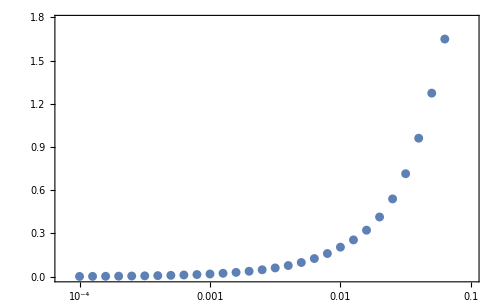

```mathematica
ListLogLinearPlot[Table[{epsilons[[i]],numePureShear[[i,1]]-intial[[1]]},{i,Length[epsilons]}]]
```

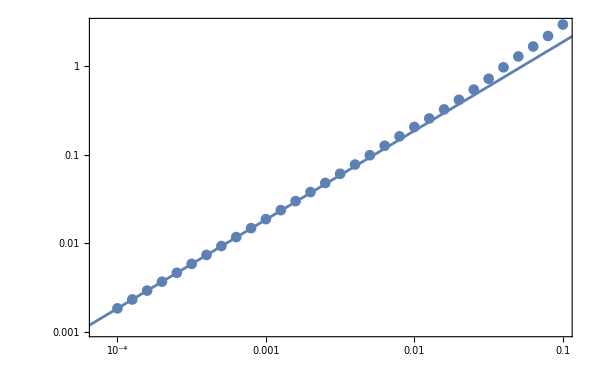

```mathematica
Show[ListLogLogPlot[Table[{epsilons[[i]],numePureShear[[i,1]]-intial[[1]]},{i,Length[epsilons]}]],LogLogPlot[x*intial[[2]],{x,0.000001,1}]]
```

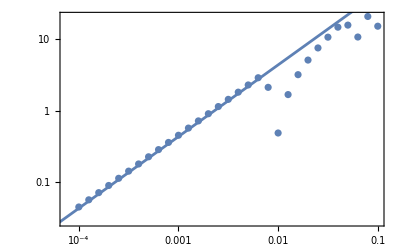

```mathematica
Show[ListLogLogPlot[Table[{epsilons[[i]],numePureShear[[i,2]]-intial[[2]]},{i,Length[epsilons]}]],LogLogPlot[x*intial[[3]],{x,0.000001,1}]]
```

## preliminary data

### load data

```mathematica
p0s={3.825}
```

{3.825}

```mathematica
temperatures={{0.063,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015}};
 records={{10}};
epsilons={{-0.01,0.,0.01},{-0.0001,0.,0.0001}};
tauEstimate={{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000}};
(*tauEstimate={{1., 2., 4. ,9. ,15. ,25., 40. ,60., 80., 120. ,200. ,300. ,1000. ,1500., 5000. ,10000.},{1., 3., 4. ,8. ,15. ,40. ,70. ,150. ,250., 600. ,2000., 2500. ,4500., 9500.},{4. ,5. ,7. ,10. ,30. ,70., 150. ,700. ,1400., 4000. ,9500.}};*)
```

```mathematica
pureShearDerivatives=Table[Table[
Table[Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/pureShear/p","/pureShearDerivatives1st2nd_N4096_p","_T","_epsilon","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],epsilons[[ep,epi]],records[[p,rec]]},{3,4,8,8,0}],"Data"],{rec,Length[records[[p]]]}],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
timeEnergy=Table[Table[
Table[Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/pureShear/p","/timeEnergy_N4096_p","_T","_epsilon","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],epsilons[[ep,epi]],records[[p,rec]]},{3,4,8,8,0}],"Data"],{rec,Length[records[[p]]]}],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

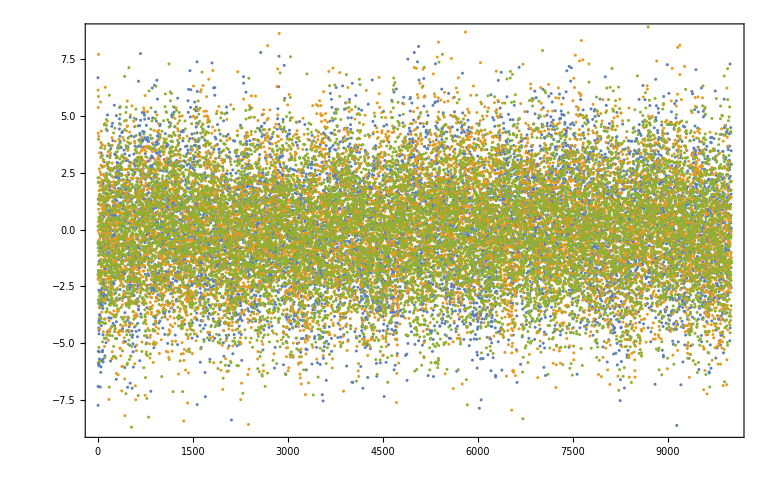

```mathematica
ListPlot[{Table[{timeEnergy[[1,12,1,1,1,1,i]],pureShearDerivatives[[1,12,1,1,1,1,i]]},{i,10000}],Table[{timeEnergy[[1,12,1,3,1,1,i]],pureShearDerivatives[[1,12,1,3,1,1,i]]},{i,10000}],Table[{timeEnergy[[1,12,1,3,1,1,i]],pureShearDerivatives[[1,12,1,2,1,1,i]]},{i,10000}]}]
```

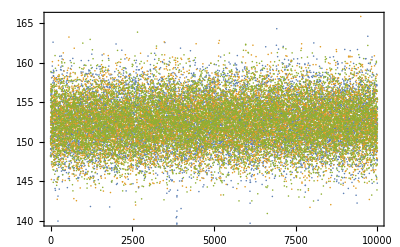

```mathematica
ListPlot[{Table[{timeEnergy[[1,12,1,1,1,1,i]],timeEnergy[[1,1,1,1,1,2,i]]},{i,10000}],Table[{timeEnergy[[1,12,1,3,1,1,i]],timeEnergy[[1,1,1,3,1,2,i]]},{i,10000}],Table[{timeEnergy[[1,12,1,3,1,1,i]],timeEnergy[[1,1,1,2,1,2,i]]},{i,10000}]}]
```

```mathematica
Dimensions[timeEnergy]
```

{1,1,2,3,1}

```mathematica
g1=Table[Table[
Table[Table[Mean[Normal[pureShearDerivatives[[p,T,ep,2,rec,2]]]],{rec,Length[records[[p]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
g1*0.05^2
```

{{{{27.0948},{27.0948}},{{21.7683},{21.7683}},{{19.5711},{19.5711}},{{14.4179},{14.4179}},{{11.7389},{11.7389}},{{10.719},{10.719}},{{9.7994},{9.7994}},{{9.05463},{9.05463}},{{8.34697},{8.34697}},{{7.88169},{7.88169}},{{7.50981},{7.50981}},{{7.18712},{7.18712}},{{6.87369},{6.87369}}}}